```mathematica
a=0;
b=1;
```

```mathematica
TestNum=1;(*один из заготовленных тестов*)
```

```mathematica
n=30;
```

```mathematica
Switch[TestNum,
1,BCleft=3;BCright=3;
λ[x_]:=10+20*x*(x-1);q[x_]:=10000*(x-0.5);
ua=0;qa=0;αa=10^5;u∞a=200;
ub=0;qb=0;αb=10^2;u∞b=300;,
2,BCleft=3;BCright=3;
λ[x_]:=10;q[x_]:=-10000*(x-0.5);
ua=0;qa=0;αa=10^2;u∞a=300;
ub=0;qb=0;αb=10^2;u∞b=300;,
3,BCleft=1;BCright=1;
λ[x_]:=1;q[x_]:=0;
ua=0;qa=0;αa=10^2;u∞a=300;
ub=1;qb=0;αb=10^2;u∞b=300;
]
```

```mathematica
paramsA={ua,qa,αa,u∞a};
paramsB={ub,qb,αb,u∞b};
```

```mathematica
BCf[BCleft_,BCright_,paramsA_,paramsB_]:=Module[{β0=10^-20},
Switch[BCleft,
1,KK[[1,1]]+=(-λλ[[1]])/β0;ff[[1]]+=(-λλ[[1]])/β0*paramsA[[1]];,
2,ff[[1]]+=-paramsA[[2]];,
3,KK[[1,1]]+=paramsA[[3]];ff[[1]]+=paramsA[[3]]*paramsA[[4]];
];
Switch[BCright,
1,KK[[n,n]]+=λλ[[n]]/β0;ff[[n]]+=λλ[[n]]/β0*paramsB[[1]];,
2,ff[[n]]+=-paramsB[[2]];,
3,KK[[n,n]]+=paramsB[[3]];
ff[[n]]+=paramsB[[3]]*paramsB[[4]];
]
]
```

```mathematica
Ne=n-1;
h=(b-a)/(n-1);
hh=Table[h,{i,Ne}];
```

```mathematica
Nodes=Table[a+hh[[i]]*i,{i,0,n-1}];
```

```mathematica
ConnectTable=Table[{e,e,e+1,Nodes[[e]],Nodes[[e+1]]},{e,Ne}];
```

```mathematica
λλ=Table[λ[Nodes[[i]]],{i,1,n}];
```

```mathematica
qq=Table[q[Nodes[[i]]],{i,1,n}];
```

```mathematica
KK=Table[0.0,{i,n},{j,n}];
```

```mathematica
ff=Table[0.0,{i,n}];
```

```mathematica
uu=Table[0.0,{i,n}];
```

```mathematica
For[k=1,k<=Ne,++k,
i=ConnectTable[[k,2]];j=ConnectTable[[k,3]];
coeff=(λλ[[i]]+λλ[[j]])/(2.0*hh[[k]]);
KK[[i,i]]+=coeff;KK[[i,j]]+=-coeff;
KK[[j,i]]+=-coeff;KK[[j,j]]+=coeff;
coeff=hh[[k]]/6.0;
ff[[i]]+=coeff*(2.0*qq[[i]]+qq[[j]]);ff[[j]]+=coeff*(qq[[i]]+2.0*qq[[j]]);
]
```

```mathematica
BCf[BCleft,BCright,paramsA,paramsB];
uu=LinearSolve[KK,ff];
```

```mathematica
BCeqLeft[c_,BC_,params_]:=Switch[BC,
1,u[c]==params[[1]],
2,(λ[c]*D[u[x],x]/.x->c)==params[[2]],
3,(λ[c]*D[u[x],x]/.x->c)==params[[3]]*(u[c]-params[[4]])]
BCeqRight[c_,BC_,params_]:=Switch[BC,
1,u[c]==params[[1]],
2,-(λ[c]*D[u[x],x]/.x->c)==params[[2]],
3,-(λ[c]*D[u[x],x]/.x->c)==params[[3]]*(u[c]-params[[4]])]
```

```mathematica
Exas=Assuming[{λ[x]>=0,λ[x]∈ Reals,q[x]∈ Reals, u[x]∈ Reals},NDSolve[{D[λ[x]*u'[x],x]+q[x]==0,
BCeqLeft[a,BCleft,paramsA],BCeqRight[b,BCright,paramsB]},u[x],{x,a,b}][[1]]];
```

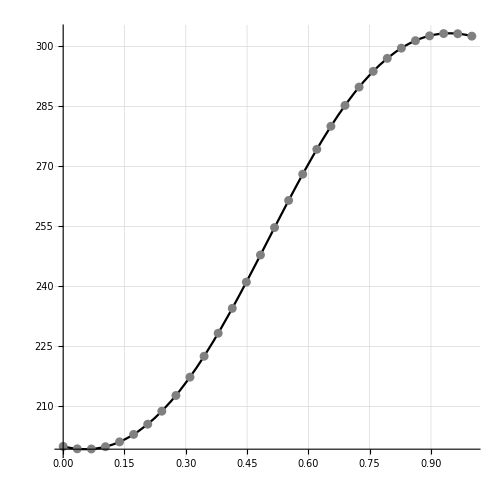

```mathematica
Show[Plot[u[x]/.Exas,{x,0,1}, PlotStyle->Black],ListPlot[Transpose@{Nodes,uu},PlotStyle->Gray],PlotRange->All,ImageSize->500,AxesStyle->Black,LabelStyle->13,GridLines->Automatic,AspectRatio->1]
```